# Heavy neutrino decays

```mathematica
<<FeynCalc`
```

FeynCalc is already loaded! If you are trying to reload FeynCalc or load FeynArts, TARCER, PHI, FeynHelpers or any other add-on, please restart the kernel.

$Aborted

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/matheushostert/Repos/nicgen

```mathematica
dm[mu_]:=GA[mu]
dm[5]:=DiracMatrix[5]
ds[p_]:=DiracSlash[p]
mt[mu_,nu_]:=MetricTensor[mu,nu]
fv[p_,mu_]:=FourVector[p,mu]
epsilon[a_,b_,c_,d_]:=LeviCivita[a,b,c,d]
id[n_]:=IdentityMatrix[n]
sp[p_,q_]:=ScalarProduct[p,q]
li[mu_]:=LorentzIndex[mu]
prop[p_,m_]:=ds[p]+m
PR=dm[6];
PL=dm[7];
dσ[μ_,ν_]:=I/2(dm[μ].dm[ν]-dm[ν].dm[μ]);
SetOptions[{DiracMatrix, DiracSlash,LeviCivita, FourVector, MetricTensor, SetMandelstam, OneLoop, ScalarProduct},Dimension->4];
```

#### Kinematics

phase space is defined as follows:
dPS^3 (k1 → k2, k3, k4) := (dm23^2 dm24^2 dΩ_4 dϕ_34)/(32 m1^2(2π)^5)
Convention: 
dm23^2 = t
	dm24^2=u
	dm34^2=v

```mathematica
Lambda[a_,b_, c_] := (a-b-c)^2-4b c
subP = {Pair[Momentum[k1],Momentum[k1]]-> m1^2,
Pair[Momentum[k2],Momentum[k2]]->m2^2,
Pair[Momentum[k3],Momentum[k3]]->m3^2,
Pair[Momentum[k4],Momentum[k4]]->m4^2,
Pair[Momentum[k1],Momentum[k2]]->(-m34sqr+m1^2+m2^2)/2,
Pair[Momentum[k1],Momentum[k3]]->-1/2(m24sqr - m1^2-m3^2),
Pair[Momentum[k1],Momentum[k4]]->(-m23sqr+m1^2+m4^2)/2,
Pair[Momentum[k2],Momentum[k3]]->(m23sqr-m2^2-m3^2)/2,
Pair[Momentum[k2],Momentum[k4]]->(m24sqr-m4^2-m2^2)/2,
Pair[Momentum[k3],Momentum[k4]]->(m34sqr-m4^2-m3^2)/2,
Pair[Momentum[s],Momentum[s]]-> -1,
Pair[Momentum[k1],Momentum[s]]-> 0,
Pair[Momentum[k2],Momentum[s]]-> k3CM*c3+k4CM*c4,
Pair[Momentum[k3],Momentum[s]]-> -k3CM *c3,
Pair[Momentum[k4],Momentum[s]]-> -k4CM*c4};

subPexpressions={
k4CM->m1/2 √ Lambda[1,m23sqr/m1^2,m4^2/m1^2],k3CM->m1/2 √ Lambda[1,m24sqr/m1^2,m3^2/m1^2],
k2CM->m1/2 √ Lambda[1,m34sqr/m1^2,m2^2/m1^2]};

subEexpressions={
E4CM->(m1^2+m4^2-m23sqr)/(2m1),E3CM->(m1^2+m3^2-m24sqr)/(2m1),
E2CM->(m1^2+m2^2-m34sqr)/(2m1)};

subC4expressions={c4-> c3*c34-√(1-c3*c3)*√(1-c34*c34)*cphi34};

subC34expressions={c34-> (m23sqr+m24sqr-m2*m2-m1*m1+2*E3CM*E4CM)/(2*k3CM*k4CM)};

subMassNorm ={m1-> 1  m1,m2-> x2 m1, m3-> x3 m1, m4 -> x4 m1, m24sqr-> x24 m1^2,m23sqr-> x23 m1^2, m34sqr-> x34 m1^2,MW-> xWBOSON m1,MZBOSON-> xZBOSON m1, MZPRIME-> xZPRIME m1};
```

#### Phase space

```mathematica
PS3 = 1/(32 m1^2 (2 π)^5);
FluxFactor=1/(2 m1);
SpinAverage = 1/2;
```

## Amplitudes

## ν_h (k1) -->l_β-(k2) l_α+(k3) v_i (k4)

```mathematica
MajAmp=( (-MT[μ,ν])/(sp[k2-k1,k2-k1] - MZBOSON^2)SpinorUBar[k2,m2].(Cih dm[μ].PL - CihC dm[μ].PR) .((1+ h dm[5].ds[s])/2).SpinorU[k1,m1] SpinorUBar[k3,m3].dm[ν].(Cv- Ca dm[5]).SpinorV[k4,m4] +  (-MT[μ,ν])/(sp[k2-k1,k2-k1] - MZPRIME^2)SpinorUBar[k2,m2].(Dih dm[μ].PL- DihC dm[μ].PR).((1+ h dm[5].ds[s])/2) . SpinorU[k1,m1] SpinorUBar[k3,m3].dm[ν].(Dv- Da dm[5]).SpinorV[k4,m4]) *NCflag+gweak^2/2((-MT[μ,ν])/(sp[k1-k3,k1-k3] - MW^2))(SpinorUBar[k2,m2].dm[μ].PL.((1+ h dm[5]. ds[s])/2).SpinorU[k1,m1] SpinorUBar[k3,m3].dm[ν].PL.SpinorV[k4,m4])*CCflag1+gweak^2/2((-MT[μ,ν])/(sp[k2+k3,k2+k3]- MW^2))(SpinorUBar[k2,m2].dm[μ].PR.((1+ h dm[5].ds[s])/2).SpinorU[k1,m1] SpinorUBar[k3,m3].dm[ν].PR.SpinorV[k4,m4])*CCflag2;
```

```mathematica
MajAmpC =((-MT[μ,ν])/(sp[k2-k1,k2-k1] - MZBOSON^2)ComplexConjugate[SpinorUBar[k2,m2].(Cih dm[μ].PL - CihC dm[μ].PR) . ((1+ h dm[5].ds[s])/2).SpinorU[k1,m1]]ComplexConjugate[  SpinorUBar[k3,m3].dm[ν].(Cv- Ca dm[5]).SpinorV[k4,m4]] +   (-MT[μ,ν])/(sp[k2-k1,k2-k1] - MZPRIME^2)ComplexConjugate[SpinorUBar[k2,m2].(Dih dm[μ].PL- DihC dm[μ].PR).((1+ h dm[5].ds[s])/2).SpinorU[k1,m1]]ComplexConjugate[  SpinorUBar[k3,m3].dm[ν].(Dv- Da dm[5]).SpinorV[k4,m4]])*NCflag+(gweak^2/2((-MT[μ,ν])/(sp[k1-k3,k1-k3] - MW^2))(ComplexConjugate[SpinorUBar[k2,m2].dm[μ].PL.((1+ h dm[5].ds[s])/2).SpinorU[k1,m1]]ComplexConjugate[ SpinorUBar[k3,m3].dm[ν].PL.SpinorV[k4,m4]])CCflag1 + gweak^2/2((-MT[μ,ν])/(sp[k2+k3,k2+k3] - MW^2))(ComplexConjugate[SpinorUBar[k2,m2].dm[μ].PR.((1+ h dm[5].ds[s])/2).SpinorU[k1,m1]]ComplexConjugate[ SpinorUBar[k3,m3].dm[ν].PR.SpinorV[k4,m4]])CCflag2) /.{μ-> μ2,ν-> ν2};
```

```mathematica
MajAmpAVE=( (-MT[μ,ν])/(sp[k2-k1,k2-k1] - MZBOSON^2)SpinorUBar[k2,m2].(Cih dm[μ].PL - CihC dm[μ].PR).SpinorU[k1,m1] SpinorUBar[k3,m3].dm[ν].(Cv- Ca dm[5]).SpinorV[k4,m4] +  (-MT[μ,ν])/(sp[k2-k1,k2-k1] - MZPRIME^2)SpinorUBar[k2,m2].(Dih dm[μ].PL- DihC dm[μ].PR).SpinorU[k1,m1] SpinorUBar[k3,m3].dm[ν].(Dv- Da dm[5]).SpinorV[k4,m4]) *NCflag+gweak^2/2((-MT[μ,ν])/(sp[k1-k3,k1-k3] - MW^2))(SpinorUBar[k2,m2].dm[μ].PL.SpinorU[k1,m1]SpinorUBar[k3,m3].dm[ν].PL.SpinorV[k4,m4])*CCflag1+gweak^2/2((-MT[μ,ν])/(sp[k2+k3,k2+k3]- MW^2))(SpinorUBar[k2,m2].dm[μ].PR.SpinorU[k1,m1] SpinorUBar[k3,m3].dm[ν].PR.SpinorV[k4,m4])*CCflag2;
```

```mathematica
MajAmpCAVE =((-MT[μ,ν])/(sp[k2-k1,k2-k1] - MZBOSON^2)ComplexConjugate[SpinorUBar[k2,m2].(Cih dm[μ].PL - CihC dm[μ].PR) .SpinorU[k1,m1]]ComplexConjugate[  SpinorUBar[k3,m3].dm[ν].(Cv- Ca dm[5]).SpinorV[k4,m4]] +   (-MT[μ,ν])/(sp[k2-k1,k2-k1] - MZPRIME^2)ComplexConjugate[SpinorUBar[k2,m2].(Dih dm[μ].PL- DihC dm[μ].PR).SpinorU[k1,m1]]ComplexConjugate[  SpinorUBar[k3,m3].dm[ν].(Dv- Da dm[5]).SpinorV[k4,m4]])*NCflag+(gweak^2/2((-MT[μ,ν])/(sp[k1-k3,k1-k3] - MW^2))(ComplexConjugate[SpinorUBar[k2,m2].dm[μ].PL.SpinorU[k1,m1]]ComplexConjugate[ SpinorUBar[k3,m3].dm[ν].PL.SpinorV[k4,m4]])CCflag1 + gweak^2/2((-MT[μ,ν])/(sp[k2+k3,k2+k3] - MW^2))(ComplexConjugate[SpinorUBar[k2,m2].dm[μ].PR.SpinorU[k1,m1]]ComplexConjugate[ SpinorUBar[k3,m3].dm[ν].PR.SpinorV[k4,m4]])CCflag2) /.{μ-> μ2,ν-> ν2};
```

## Spin sums and Trace

```mathematica
MajAmpSQR = FermionSpinSum[MajAmpC MajAmp]//Simplify;
```

```mathematica
TracedMajAmpSQR = MajAmpSQR/.{DiracTrace-> Tr}/.{k4-> k1 -k2-k3}//Contract
```

-(CCflag1^2 (OverBar[k1]·OverBar[k2]) (OverBar[k1]·OverBar[k3]-OverBar[k2]·OverBar[k3]-OverBar[k3]^2) gweak^4)/(2 (MW^2-OverBar[k1]^2+2 (OverBar[k1]·OverBar[k3])-OverBar[k3]^2)^2)+1406+(4 Da^2 DihC^2 NCflag^2 (OverBar[k1]·OverBar[k2]) (OverBar[k1]·OverBar[k3]))/((MZPRIME^2-OverBar[k1]^2+2 (OverBar[k1]·OverBar[k2])-OverBar[k2]^2)^2)+(4 Dih^2 Dv^2 NCflag^2 (OverBar[k1]·OverBar[k2]) (OverBar[k1]·OverBar[k3]))/((MZPRIME^2-OverBar[k1]^2+2 (OverBar[k1]·OverBar[k2])-OverBar[k2]^2)^2)+(4 DihC^2 Dv^2 NCflag^2 (OverBar[k1]·OverBar[k2]) (OverBar[k1]·OverBar[k3]))/((MZPRIME^2-OverBar[k1]^2+2 (OverBar[k1]·OverBar[k2])-OverBar[k2]^2)^2)
 |  |  |  |

```mathematica
MajAmpSQRAVERAGED = FermionSpinSum[MajAmpCAVE MajAmpAVE]//Simplify;
```

```mathematica
TracedMajAmpSQRAVERAGED = MajAmpSQRAVERAGED/.{DiracTrace-> Tr}/.{k4-> k1 -k2-k3}//Contract;
```

#### Generic substitutions

```mathematica
subMasslessNorm={x2-> 0, x3->0,x4-> 0};
subMassless={m2-> 0, m3->0,m4-> 0};
subGf={gweak-> √((8 Gf MW^2)/(√2))};subGfNC={gweak-> √((8 Gf cw^2 MZBOSON^2)/(√2))};
subAlphaQED={eQED-> √(alphaQED*4π)};
subINTEGRATION={m34sqr-> m1^2+m2^2+m3^2+m4^2-u-t, m23sqr-> t , m24sqr-> u };
subINVtoCMenergies={u-> m1^2-2 m1 Eplus,t->- m1^2 + 2m1 (Eplus+Eminus) };
subgLgR=(Solve[Ca== gL-gR&&Cv==gL+gR,{gL,gR}])[[1]];
subVAtoLR={Ca->  gL-gR,Cv-> gL+gR};
subCvCa={Ca-> -1/2,Cv-> (-1/2+2 Sin[W]^2)};
subCW=(Solve[Gf/(√2)-gweak^2/(8 cw^2 MZBOSON^2)==0,{cw}]//Simplify//PowerExpand)[[1]];
submasses={m4-> 0,m3-> mlep, m2-> mlep, m23sqr-> t, m24sqr-> u};
subMasslessNorm={x2-> 0, x3->0,x4-> 0};
subMassless={m2-> 0, m3->0,m4-> 0};
```

#### Substitutions of special cases

```mathematica
subFULL={CihC-> Cih, DihC-> Dih};
(**)subNConly={Dv-> 0, Da-> 0,Dih-> 0,DihC-> 0,Cih-> Umixing gweak/(2Cos[W]),CihC-> Umixing gweak/(2Cos[W]),Ca-> gweak/(2cw)( gL-gR),Cv-> gweak/(2cw)(gL+gR),CCflag1-> 0,CCflag2-> 0, NCflag-> (MZBOSON^2-m23sqr)/MZBOSON^2,DIP-> 0};
(**)
subNCplusCC={Dv-> 0, Da-> 0,Dih-> 0,DihC-> 0,Cih-> Umixing gweak/(2Cos[W]),CihC-> Umixing gweak/(2Cos[W]),Ca->gweak/(2cw)( gL-gR),Cv-> gweak/(2cw)(gL+gR),CCflag1-> (Umixing(MW^2-m34sqr))/MW^2,CCflag2-> -Umixing(MW^2-m24sqr)/MW^2, NCflag-> (MZBOSON^2-m23sqr)/MZBOSON^2,DIP-> 0};
(**)
subCConly={Dv-> 0, Da-> 0,Cih-> 0,CCflag1-> (Umixing(MW^2-m34sqr))/MW^2,CCflag2->Umixing(MW^2-m23sqr)/MW^2, NCflag-> 0,DIP-> 0};
(**)
subBSMonly={CCflag1-> 0,CCflag2-> 0,Cv-> 0,Ca-> 0,NCflag-> (MZPRIME^2-m34sqr)/MZPRIME^2,Da-> 0,Dih-> Umixing √(alphaD*4π) ,Dv-> √(alphaQED*4π) eps,dij-> 0};
(**)
subDIPOLEonly={CCflag1-> 0,CCflag2-> 0,Cv-> 0,Ca-> 0,NCflag-> 0,Da-> 0,Dih->0 ,Dv-> 0,DIP-> 1};
```

## Full Expression

```mathematica
FULLAVERAGED = TracedMajAmpSQRAVERAGED* PS3*FluxFactor*SpinAverage*4 π^2*2/.subFULL/.subP/.subPexpressions/.subINTEGRATION//ExpandAll//Cancel;
```

```mathematica
FULL = TracedMajAmpSQR* PS3*FluxFactor*4 π^2*2/.subFULL/.subP/.subPexpressions/.subINTEGRATION//ExpandAll//Cancel;
```

```mathematica
Unprotect[Power];
Format[Power[a_,n_Integer?Positive],CForm]:=Distribute[ConstantArray[Hold[a],n],Hold,List,HoldForm,Times]
Protect[Power];
```

```mathematica
Export["DecayRates/NtoNuLL.dat",CForm[FULLAVERAGED]];
Export["DecayRates/NtoNuLL_helicity.dat",CForm[FULL]];
```

### Obtaning simple formula in the massless case with contact Z’ interaction

#### Contact propagator

```mathematica
simpBSM=((FULL/.subBSMonly))/.subINTEGRATION/.subMassless//FullSimplify
simpMasses=((FULL/.subBSMonly))/.subINTEGRATION/.{t-> m23sqr,u-> m24sqr}//FullSimplify
```

(alphaD alphaQED eps^2 (h^2+1) Umixing^2 (m1^2 (t+u)-t^2-u^2))/(8 π m1^3 MZPRIME^4)

1/(8 π m1^3 MZPRIME^4)alphaD alphaQED eps^2 (h^2+1) Umixing^2 (2 m1^3 m2+m1^2 (-2 m2^2+m23sqr+m24sqr-m3^2-m4^2)+2 m1 m2 (m2^2-m23sqr-m24sqr+4 m3 m4)+m2^2 (m23sqr+m24sqr-m3^2-m4^2)-m23sqr^2+m4^2 (m23sqr+m24sqr-2 m3^2)+2 m3 m4 (m23sqr+m24sqr-m3^2)+m23sqr m3^2-m24sqr^2+m24sqr m3^2-2 m3 m4^3)

```mathematica
SMonly = FULL/.{h^2-> 1,Dih-> 0,m24sqr-> u,m23sqr-> t,m3-> mlep,m4-> mlep,CCflag1-> CC,CCflag2-> -CC};
```

```mathematica
int = Integrate[Integrate[simpBSM,{u,0,m1^2-t}],{t,0,m1^2}]/.{Dih-> Subscript[U, mu4] gD ,Dv-> eQED eps}/.{eQED->√(alphaQED*4π),gD->√(alphaD*4π) }
```

(alphaD alphaQED eps^2 (h^2+1) m1^5 Umixing^2)/(48 π MZPRIME^4)

```mathematica
int/.{alphaD-> gx^2/4/π,alphaQED-> eQED^2/4/π}
```

(eps^2 eQED^2 gx^2 (h^2+1) m1^5 Umixing^2)/(768 π^3 MZPRIME^4)

### Export simple integrand to file (used in monophoton code)

```mathematica
BSMonly = FULL*2/.{h^2-> 1,CCflag1-> 0,CCflag2-> 0,Cih-> 0,Cv-> 0,Ca-> 0,Da-> 0,Dih-> UD5 UD4 ,Dv-> eQED eps,MZPRIME-> mzprime,NCflag-> 1}/.{eQED->√(alphaQED*4π),gD->√(alphaD*4π) }/.subINTEGRATION//Simplify

BSMonly/.{t-> mm^2+mp^2+mh^2+mf^2-u-v}//Simplify

Export["N_diff_rate_BSMonly.dat",CForm[BSMonly]/.{Pi->pi}];
```

(alphaQED eps^2 UD4^2 UD5^2 (2 m1^3 m2+m1^2 (-2 m2^2-m3^2-m4^2+t+u)+2 m1 m2 (m2^2+4 m3 m4-t-u)+m2^2 (-m3^2-m4^2+t+u)-2 m3^3 m4-2 m3^2 m4^2+m3^2 t+m3^2 u-2 m3 m4^3+2 m3 m4 t+2 m3 m4 u+m4^2 t+m4^2 u-t^2-u^2))/(8 π^2 m1^3 (m1^2+m2^2+m3^2+m4^2-mzprime^2-t-u)^2)

(alphaQED eps^2 UD4^2 UD5^2 (2 m1^3 m2+m1^2 (-2 m2^2-m3^2-m4^2+mf^2+mh^2+mm^2+mp^2-v)+2 m1 m2 (m2^2+4 m3 m4-mf^2-mh^2-mm^2-mp^2+v)+m2^2 (-m3^2-m4^2+mf^2+mh^2+mm^2+mp^2-v)-2 m3^3 m4-2 m3^2 m4^2+m3^2 (mf^2+mh^2+mm^2+mp^2-u-v)+m3^2 u-2 m3 m4^3+2 m3 m4 (mf^2+mh^2+mm^2+mp^2-u-v)+2 m3 m4 u+m4^2 (mf^2+mh^2+mm^2+mp^2-u-v)+m4^2 u-(mf^2+mh^2+mm^2+mp^2-u-v)^2-u^2))/(8 π^2 m1^3 (m1^2+m2^2+m3^2+m4^2-mf^2-mh^2-mm^2-mp^2-mzprime^2+v)^2)

#### Check CC only

```mathematica
CConlyHel = FULLAVERAGED*((t-MW^2)^2)/MW^4/.{h^2-> 1,Cih-> 0,Dih-> 0,m24sqr-> u,m23sqr-> t,m2 -> 0,m3-> 0,m4-> mlep,CCflag1-> 0,CCflag2-> 1}//Simplify;
CConly = ((CConlyHel/.{h-> 1})+(CConlyHel/.{h-> -1}))/2//Simplify
```

(gweak^4 t (m1^2+mlep^2-t))/(512 π^3 m1^3 MW^4)

```mathematica
Integrate[Integrate[CConly,{t,0,m1^2-u}],{u,0,m1^2}]/.{mlep-> 0}/.subGf//Simplify
```

(Gf^2 m1^5)/(192 π^3)

### Full propagators

#### integral over m24sqr

```mathematica
fullIntegrand = FULL*MZPRIME^4/(MZPRIME^2-m34sqr)^2/.subBSMonly/.{m1-> mh,m2-> 0,m3->0,m4->0}/.{t-> m23sqr,u-> m24sqr}/.{m34sqr->mh^2-m24sqr-m23sqr}//Simplify
```

-(alphaD alphaQED eps^2 (h^2+1) Umixing^2 (m23sqr^2-m23sqr mh^2+m24sqr (m24sqr-mh^2)))/(8 π mh^3 (m23sqr+m24sqr-mh^2+MZPRIME^2)^2)

```mathematica
int2=Integrate[fullIntegrand,{m24sqr,0,mh^2-m23sqr}]//Normal//FullSimplify//PowerExpand//Simplify
```

-(alphaD alphaQED eps^2 (h^2+1) Umixing^2 ((m23sqr-mh^2) (m23sqr (1/(m23sqr-mh^2+MZPRIME^2)-2/MZPRIME^2)-2)-(2 m23sqr-mh^2+2 MZPRIME^2) (2 log(MZPRIME)-log(m23sqr-mh^2+MZPRIME^2))))/(8 π mh^3)

```mathematica
int2BW=Integrate[FULL((m23sqr+m24sqr-m1^2+MZPRIME^2)^2)/((m23sqr+m24sqr-m1^2+MZPRIME^2)^2+MZPRIME^2 TOTRATE^2)/.subBSMonly//Simplify,{m24sqr,0,mh^2-m23sqr},Assumptions->subPositive]//Normal//FullSimplify//PowerExpand//Simplify
```

$Aborted

```mathematica
FULL((m23sqr+m24sqr-m1^2+MZPRIME^2)^2)/((m23sqr+m24sqr-m1^2+MZPRIME^2)^2+MZPRIME^2 TOTRATE^2)/.subBSMonly//Simplify
```

(alphaD alphaQED eps^2 (h^2+1) Umixing^2 (m34sqr-MZPRIME^2)^2 (-m1^2+m23sqr+m24sqr+MZPRIME^2)^2 (2 m1^3 m2+m1^2 (-2 m2^2-m3^2-m4^2+t+u)+2 m1 m2 (m2^2+4 m3 m4-t-u)+m2^2 (-m3^2-m4^2+t+u)-2 m3^3 m4-2 m3^2 m4^2+m3^2 t+m3^2 u-2 m3 m4^3+2 m3 m4 t+2 m3 m4 u+m4^2 t+m4^2 u-t^2-u^2))/(8 π m1^3 MZPRIME^4 (m1^4-2 m1^2 (m23sqr+m24sqr+MZPRIME^2)+m23sqr^2+2 m23sqr (m24sqr+MZPRIME^2)+m24sqr^2+2 m24sqr MZPRIME^2+MZPRIME^4+MZPRIME^2 TOTRATE^2) (m1^2+m2^2+m3^2+m4^2-MZPRIME^2-t-u)^2)

#### integral over m23sqr

```mathematica
int3=Integrate[int2,{m23sqr,0,mh^2}]
```

ConditionalExpression[-1/(8 π mh^3)alphaD alphaQED eps^2 (h^2+1) Umixing^2 (mh^6/(3 MZPRIME^2)+mh^4-2 mh^2 MZPRIME^2+2 MZPRIME^2 ((mh-MZPRIME) (mh+MZPRIME) log(MZPRIME^2-mh^2)-2 mh^2 log(MZPRIME)+MZPRIME^2 log(MZPRIME^2))), ]

```mathematica
int3BW=Integrate[int2BW,{m23sqr,0,mh^2}]
```

int2BW mh^2

```mathematica
final = FullSimplify[int3/.{Dih-> Subscript[U, mu4] gD ,Dv-> eQED eps}/.{eQED->√(alphaQED*4π),gD->√(alphaD*4π) },Assumptions->{MZZPRIME>mh,mh> 0,MZPRIME>0}]/.{alphaD-> Valpha4alphaepsilon2/eps^2/alphaQED/Subscript[U, mu4]^2}//Normal
```

((h^2+1) mh^4 Umixing^2 Valpha4alphaepsilon2 (m34sqr-MZPRIME^2)^2 (2 m1^3 m2+m1^2 (-2 m2^2-m3^2-m4^2+t+u)+2 m1 m2 (m2^2+4 m3 m4-t-u)+m2^2 (-m3^2-m4^2+t+u)-2 m3^3 m4-2 m3^2 m4^2+m3^2 t-2 m3 m4^3+2 m3 m4 t+u (m3+m4)^2+m4^2 t-t^2-u^2))/(16 π m1^3 MZPRIME^4 U_mu4^2 (m1^2+m2^2+m3^2+m4^2-MZPRIME^2-t-u)^2)

### Simplify full propagator

```mathematica
TotGamma = int3 /.h^2-> 1/.MZPRIME-> mh/√r//Simplify//Normal//FullSimplify
```

-(alphaD alphaQED eps^2 mh Umixing^2 (6 log(mh^2/r)+6 (r-1) log(-(mh^2 (r-1))/r)+r (-12 log(mh/(√r))+r (r+3)-6)))/(12 π r^2)

```mathematica
Series[TotGamma*r^2,{r,0,4}]//PowerExpand
```

(alphaD alphaQED eps^2 mh r^4 Umixing^2)/(24 π)+O(r^5)

```mathematica
Series[Log[1/(1-x)],{x,0,10}]
```

x+x^2/2+x^3/3+x^4/4+x^5/5+x^6/6+x^7/7+x^8/8+x^9/9+x^10/10+O(x^11)

```mathematica
-(r (r (r+3)-6)-6(1-r) log(1-r)//Factor)//Simplify
```

-r (r^2+3 r-6)-6 (r-1) log(1-r)

### Simplify full propagator w/ B-W

```mathematica
finalBW =Simplify[ int3BW/.{Dih-> Subscript[U, mu4] gD ,Dv-> eQED eps}/.{eQED->√(alphaQED*4π),gD->√(alphaD*4π) },Assumptions->subPositive]/.{alphaD-> Valpha4alphaepsilon2/eps^2/alphaQED/Subscript[U, mu4]^2}//Normal
```

1/(48 π mh^3 MZPRIME TOTRATE)ⅈ Valpha4alphaepsilon2 (4 mh^2 MZPRIME^2 (MZPRIME-ⅈ TOTRATE)^2-4 mh^2 MZPRIME^2 (MZPRIME+ⅈ TOTRATE)^2+2 (mh^2-MZPRIME (MZPRIME-ⅈ TOTRATE))^2 (mh^2+2 MZPRIME (MZPRIME-ⅈ TOTRATE)) (log(-mh^2+MZPRIME^2-ⅈ MZPRIME TOTRATE)-log(MZPRIME (MZPRIME-ⅈ TOTRATE)))+2 (mh^2-MZPRIME (MZPRIME+ⅈ TOTRATE))^2 (mh^2+2 MZPRIME (MZPRIME+ⅈ TOTRATE)) (-log(-mh^2+MZPRIME^2+ⅈ MZPRIME TOTRATE)+log(MZPRIME+ⅈ TOTRATE)+log(MZPRIME))+mh^4 (-MZPRIME) (MZPRIME-ⅈ TOTRATE)+mh^4 MZPRIME (MZPRIME+ⅈ TOTRATE)+6 ⅈ mh^4 MZPRIME TOTRATE)

### Simplifying the BW expression

```mathematica
/.Complex[0,n_]:> n*Icomplex
```

```mathematica
finalBWsimple = FullSimplify[(finalBW/.Arg[num_]:>ArcTan[ComplexExpand[Im[num]]/ComplexExpand[Re[num]]])/.Log[Z_]:> Log[Re[Z]^2+Im[Z]^2]/2+I* ArcTan[Im[Z]/Re[Z]],Assumptions->subPositive]/.Icomplex-> I
```

1/(48 π mh^3 MZPRIME TOTRATE)ⅈ Valpha4alphaepsilon2 ((mh^2-MZPRIME (MZPRIME+ⅈ TOTRATE))^2 (mh^2+2 MZPRIME (MZPRIME+ⅈ TOTRATE)) (-log((mh^2-MZPRIME^2)^2+MZPRIME^2 TOTRATE^2)+2 ⅈ tan^-1((MZPRIME TOTRATE)/(mh^2-MZPRIME^2))+log(MZPRIME^2+TOTRATE^2)+2 ⅈ tan^-1(TOTRATE/MZPRIME)+2 log(MZPRIME))+(mh^2-MZPRIME (MZPRIME-ⅈ TOTRATE))^2 (mh^2+2 MZPRIME (MZPRIME-ⅈ TOTRATE)) (log((mh^2-MZPRIME^2)^2+MZPRIME^2 TOTRATE^2)+2 ⅈ tan^-1((MZPRIME TOTRATE)/(mh^2-MZPRIME^2))-2 log(MZPRIME (MZPRIME-ⅈ TOTRATE)))+4 mh^2 MZPRIME^2 (MZPRIME-ⅈ TOTRATE)^2-4 mh^2 MZPRIME^2 (MZPRIME+ⅈ TOTRATE)^2+8 ⅈ mh^4 MZPRIME TOTRATE)

```mathematica
Log[(-Icomplex MZPRIME TOTRATE-mh^2+MZPRIME^2)/(Icomplex MZPRIME TOTRATE-mh^2+MZPRIME^2)]/.{MZPRIME-> mh/r,TOTRATE-> mh/rprime}/.{r-> 1,rprime-> 0.01,Icomplex-> I}//FullSimplify
```

0.+3.14159 ⅈ

```mathematica
finalBWsimple=(FullSimplify[Simplify[ComplexExpand[finalBW,TargetFunctions->{Re,Im}],Assumptions->subPositive]//ExpandAll])/.Arg[num_]:>ArcTan[ComplexExpand[Im[num]]/ComplexExpand[Re[num]]]
```

1/(24 π mh^3 MZPRIME TOTRATE)Valpha4alphaepsilon2 (3 mh^2 MZPRIME^2 TOTRATE^2 tan^-1(MZPRIME^2-mh^2,MZPRIME TOTRATE)-2 ⅈ MZPRIME^3 TOTRATE^3 tan^-1(MZPRIME^2-mh^2,MZPRIME TOTRATE)-6 MZPRIME^4 TOTRATE^2 tan^-1(MZPRIME^2-mh^2,MZPRIME TOTRATE)+mh^6 tan^-1(MZPRIME^2-mh^2,MZPRIME TOTRATE)-3 mh^2 MZPRIME^4 tan^-1(MZPRIME^2-mh^2,MZPRIME TOTRATE)-6 ⅈ mh^2 MZPRIME^3 TOTRATE tan^-1(MZPRIME^2-mh^2,MZPRIME TOTRATE)-(mh^2+2 MZPRIME (MZPRIME-ⅈ TOTRATE)) (mh^2-MZPRIME^2+ⅈ MZPRIME TOTRATE)^2 tan^-1(MZPRIME^2-mh^2,-MZPRIME TOTRATE)+2 MZPRIME^6 tan^-1(MZPRIME^2-mh^2,MZPRIME TOTRATE)+6 ⅈ MZPRIME^5 TOTRATE tan^-1(MZPRIME^2-mh^2,MZPRIME TOTRATE)+6 mh^2 MZPRIME^3 TOTRATE log(MZPRIME^2+TOTRATE^2)-2 MZPRIME^3 TOTRATE (3 mh^2-3 MZPRIME^2+TOTRATE^2) log((mh^2-MZPRIME^2)^2+MZPRIME^2 TOTRATE^2)-2 (3 mh^2 MZPRIME^2 (TOTRATE^2-MZPRIME^2)+mh^6+2 MZPRIME^4 (MZPRIME^2-3 TOTRATE^2)) tan^-1(TOTRATE/MZPRIME)+8 mh^2 MZPRIME^3 TOTRATE+12 mh^2 MZPRIME^3 TOTRATE log(MZPRIME)-4 mh^4 MZPRIME TOTRATE+4 MZPRIME^3 TOTRATE^3 log(MZPRIME)+2 MZPRIME^3 TOTRATE^3 log(MZPRIME^2+TOTRATE^2)-6 MZPRIME^5 TOTRATE log(MZPRIME^2+TOTRATE^2)-12 MZPRIME^5 TOTRATE log(MZPRIME))

#### exporting it to file

```mathematica
myexp=StringReplace[ToString[CForm[finalBWsimple/.{MZPRIME-> mz,mh-> m4,TOTRATE-> GammaZprime}] ],{"ArcTan"-> "np.arctan","Log"-> "np.log","Pi"-> "np.pi"}]
Export["N_tot_decay_rate_BSMonly.dat",myexp/.{Pi->pi}];
```

```mathematica
"(Valpha4alphaepsilon2*(-4*GammaZprime*(m4*m4*m4*m4)*mz + 8*GammaZprime*(m4*m4)*(mz*mz*mz) - 2*(m4*m4*m4*m4*m4*m4 + 3*(m4*m4)*(mz*mz)*(GammaZprime*GammaZprime - mz*mz) + 2*(mz*mz*mz*mz)*(-3*(GammaZprime*GammaZprime) + mz*mz))*np.arctan(GammaZprime/mz) - (m4*m4 + Complex(0,1)*GammaZprime*mz - mz*mz)*(m4*m4 + Complex(0,1)*GammaZprime*mz - mz*mz)*(m4*m4 + 2*mz*(Complex(0,-1)*GammaZprime + mz))*np.arctan(-(m4*m4) + mz*mz,-(GammaZprime*mz)) + m4*m4*m4*m4*m4*m4*np.arctan(-(m4*m4) + mz*mz,GammaZprime*mz) + 3*(GammaZprime*GammaZprime)*(m4*m4)*(mz*mz)*np.arctan(-(m4*m4) + mz*mz,GammaZprime*mz) - Complex(0,2)*(GammaZprime*GammaZprime*GammaZprime)*(mz*mz*mz)*np.arctan(-(m4*m4) + mz*mz,GammaZprime*mz) - Complex(0,6)*GammaZprime*(m4*m4)*(mz*mz*mz)*np.arctan(-(m4*m4) + mz*mz,GammaZprime*mz) - 6*(GammaZprime*GammaZprime)*(mz*mz*mz*mz)*np.arctan(-(m4*m4) + mz*mz,GammaZprime*mz) - 3*(m4*m4)*(mz*mz*mz*mz)*np.arctan(-(m4*m4) + mz*mz,GammaZprime*mz) + Complex(0,6)*GammaZprime*(mz*mz*mz*mz*mz)*np.arctan(-(m4*m4) + mz*mz,GammaZprime*mz) + 2*(mz*mz*mz*mz*mz*mz)*np.arctan(-(m4*m4) + mz*mz,GammaZprime*mz) + 4*(GammaZprime*GammaZprime*GammaZprime)*(mz*mz*mz)*np.log(mz) + 12*GammaZprime*(m4*m4)*(mz*mz*mz)*np.log(mz) - 12*GammaZprime*(mz*mz*mz*mz*mz)*np.log(mz) + 2*(GammaZprime*GammaZprime*GammaZprime)*(mz*mz*mz)*np.log(GammaZprime*GammaZprime + mz*mz) + 6*GammaZprime*(m4*m4)*(mz*mz*mz)*np.log(GammaZprime*GammaZprime + mz*mz) - 6*GammaZprime*(mz*mz*mz*mz*mz)*np.log(GammaZprime*GammaZprime + mz*mz) - 2*GammaZprime*(mz*mz*mz)*(GammaZprime*GammaZprime + 3*(m4*m4) - 3*(mz*mz))*np.log(GammaZprime*GammaZprime*(mz*mz) + (m4*m4 - mz*mz)*(m4*m4 - mz*mz))))/(2*GammaZprime*(m4*m4*m4)*mz*np.pi)"
```

#### Running some tests as a function of m4 and mzprime

```mathematica
Taylorprop[mh_,MZPRIME_,Valpha4alphaepsilon2_]:=Evaluate[Series[final/.{Dih-> Subscript[U, mu4] gD ,Dv-> eQED eps}/.{eQED->√(alphaQED*4π),gD->√(alphaD*4π) },{MZPRIME,Infinity,10}]//Normal];
```

```mathematica
TaylorpropBW[mh_,MZPRIME_,Valpha4alphaepsilon2_,TOTRATE_]:=Evaluate[Series[finalBW/.{Dih-> Subscript[U, mu4] gD ,Dv-> eQED eps}/.{eQED->√(alphaQED*4π),gD->√(alphaD*4π) },{MZPRIME,Infinity,10}]//Normal];TaylorpropBWsimple[mh_,MZPRIME_,Valpha4alphaepsilon2_,TOTRATE_]:=Evaluate[Series[Limit[finalBWsimple,TOTRATE-> 0]/.{Dih-> Subscript[U, mu4] gD ,Dv-> eQED eps}/.{eQED->√(alphaQED*4π),gD->√(alphaD*4π) },{MZPRIME,Infinity,20}]//Normal];
```

$Aborted

```mathematica
func[mh_,MZPRIME_,Valpha4alphaepsilon2_]:=Evaluate[final]
funcBW[mh_,MZPRIME_,Valpha4alphaepsilon2_,TOTRATE_]:=Evaluate[finalBW]
funcBWsimple[mh_,MZPRIME_,Valpha4alphaepsilon2_,TOTRATE_]:=Evaluate[finalBWsimple]
```

```mathematica
Gammalight[mN_,mzprime_,Valpha4alphaepsilon2_]:=(Valpha4alphaepsilon2*mN^3)/(2 mzprime^2)*(1-(mzprime/mN)^2)^2(1/2+(mzprime/mN)^2)*HeavisideTheta[mN-mzprime,1]
```

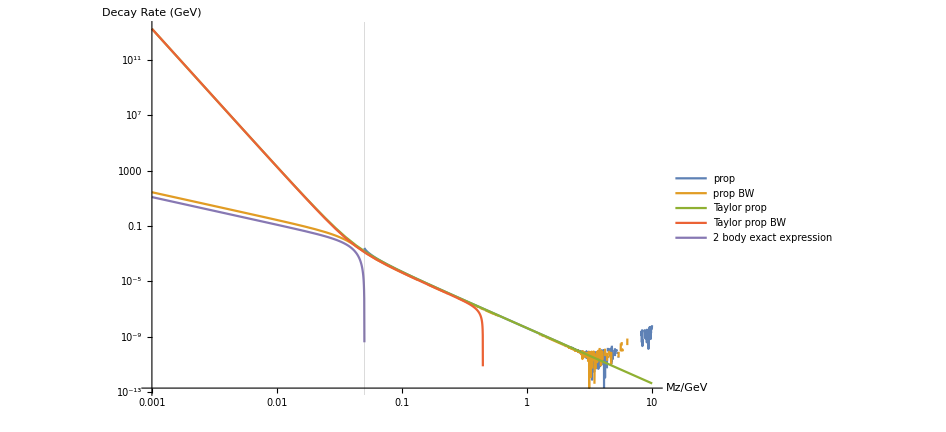

```mathematica
myM4=0.05;LogLogPlot[{func[myM4,x,1],funcBWsimple[myM4,x,1,x/3],Taylorprop[myM4,x,1],TaylorpropBW[myM4,x,1,x/3],0.4*Gammalight[myM4,x,1]},{x,0.001,10},PlotLegends->{"prop","prop BW","Taylor prop","Taylor prop BW","2 body exact expression"},AxesLabel->{"Mz/GeV","Decay Rate (GeV)"},GridLines->{{myM4},{0}},ImageSize->700]
```

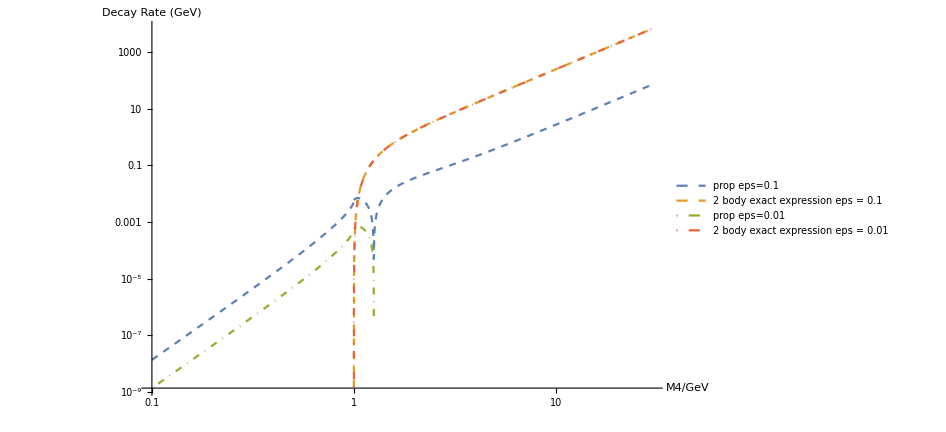

```mathematica
myMZ=1;epsilon=0.1;epsilon2=0.01;
LogLogPlot[{Abs[funcBWsimple[x,myMZ,epsilon,epsilon myMZ/3]],(Gammalight[x,myMZ,1]),funcBWsimple[x,myMZ,epsilon2,epsilon2 myMZ/3],(Gammalight[x,myMZ,1])},{x,0.1,30},PlotLegends->Placed[{"prop eps=0.1","2 body exact expression eps = 0.1","prop eps=0.01","2 body exact expression eps = 0.01"},{0.24,0.8}],AxesLabel->{"M4/GeV","Decay Rate (GeV)"},GridLines->{{0myMZ},{0}},ImageSize->700,PlotStyle->{Dashed,Dashed,DotDashed,DotDashed}]
```

```mathematica
Series[(r-r^2/2-Log[(1/(1-r))^(1-r)])*6-r^3,{r,0,5}]
```

r^4/2+(3 r^5)/10+O(r^6)

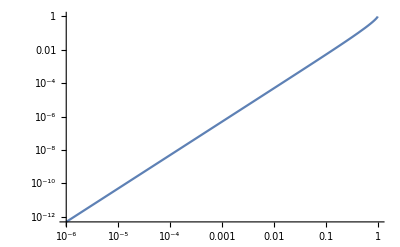

```mathematica
LogLogPlot[x-Log[(1/(1-x))^(1-x)],{x,0.000001,0.999999}]
```

```mathematica
Log[1/(1+100)]//N
```

-4.61512

$Aborted